CSE 577 * Advanced Geometric Modeling
Instructor: Dianne Hansford
Student:Yu-Hsuan, Chuang
Student ID:1211219305
Homework 3: Experimenting with NURBS
Due 6 April 2017 by midnight

Part 1. Cross Ratio
Section1:
- Implement:
cr(a, b, c, d) = [(b - a) / (d - b)] / [(c - a) / (d - c)]
The first red point from the left to right is point a, c and d respectively. The green point is point b, which is allowed to move.
- Discussion: 
If point b equal to point d, it would cause a fault because the denominator of ratio1 is 0. So, this condition should be avoided.

```mathematica
dataset = {{1,0},{3,0},{7,0}, {10,0}};
Manipulate[(
dataset[[2]]={pointb, 0};
ratio1 = EuclideanDistance[dataset[[2]],dataset[[1]]]/EuclideanDistance[dataset[[4]],dataset[[2]]];
ratio2 = EuclideanDistance[dataset[[3]],dataset[[1]]]/EuclideanDistance[dataset[[4]],dataset[[3]]];
crossratio = ratio1/ratio2;
line=Graphics[{Red,Line[dataset],Red,PointSize[0.025],Point[dataset]}];
point=Graphics[{Green,PointSize[0.025],Point[dataset[[2]]]}];
TableForm[{dataset[[1]],dataset[[2]],dataset[[3]],dataset[[4]]},TableHeadings->{ {"a","b","c", "d"},{"x", "y"}}]
TableForm[{{ratio1, ratio2, crossratio}},TableHeadings->{ {"value"},{"ratio(a,b,d)", "ratio(a,c,d)","cr(a,b,c,d)"}}]
Show[{ line,point }, Axes->True, Boxed->False, PlotRange->All, ImageSize->Medium])
,{{pointb, 3, "Point b"}, -5, 20, 1}]
```

Section2:
- Implement:
Create 4 line that have same start point (0,0) and the 5th line that cross the 4 line. The intersect points are a, b, c and d respectively.
Then compute the cross ratio (a,b,c,d). 
- Discussion: 
We can find that no matter how the 5th line change, the cross ratio maintains the same value. That’s because the cross ratio depends on the angles : [ sin(angle(aob))/ sin(angle(bod)) ] / [ sin(angle(aoc)/ sin(angle(cod)] and are thus equal.

```mathematica
dataA={{0,0},{4,8}};
dataB={{0,0},{8,8}};
dataC={{0,0},{12,8}};
dataD={{0,0},{16,8}};
data={{5,0},{0,5}};

lineA=Graphics[{Black,Line[dataA],PointSize[0.01],Point[dataA]}];
lineB=Graphics[{Black,Line[dataB],PointSize[0.01],Point[dataB]}];
lineC=Graphics[{Black,Line[dataC],PointSize[0.01],Point[dataC]}];
lineD=Graphics[{Black,Line[dataD],PointSize[0.01],Point[dataD]}];
Manipulate[(
data[[1]][[1]]=first;
data[[2]][[2]]=last;
line=Graphics[{Red,Line[data],PointSize[0.01],Point[data]}];
vector=data[[2]]-data[[1]];
iA=-(2*data[[1]][[1]]-data[[1]][[2]])/(2*vector[[1]]-vector[[2]]);
iB=-(data[[1]][[1]]-data[[1]][[2]])/(vector[[1]]-vector[[2]]);
iC=-((2/3)*data[[1]][[1]]-data[[1]][[2]])/((2/3)*vector[[1]]-vector[[2]]);
iD=-((1/2)*data[[1]][[1]]-data[[1]][[2]])/((1/2)*vector[[1]]-vector[[2]]);
pointA={data[[1]][[1]]+iA*vector[[1]], data[[1]][[2]]+iA*vector[[2]]};
POINTA=Graphics[{Blue,PointSize[0.02],Point[pointA]}];
pointB={data[[1]][[1]]+iB*vector[[1]], data[[1]][[2]]+iB*vector[[2]]};
POINTB=Graphics[{Blue,PointSize[0.02],Point[pointB]}];
pointC={data[[1]][[1]]+iC*vector[[1]], data[[1]][[2]]+iC*vector[[2]]};
POINTC=Graphics[{Blue,PointSize[0.02],Point[pointC]}];
pointD={data[[1]][[1]]+iD*vector[[1]], data[[1]][[2]]+iD*vector[[2]]};
POINTD=Graphics[{Blue,PointSize[0.02],Point[pointD]}];

ratio1 = EuclideanDistance[pointB,pointA]/EuclideanDistance[pointD,pointB];
ratio2 = EuclideanDistance[pointC,pointA]/EuclideanDistance[pointD,pointC];
crossratio = ratio1/ratio2;
TableForm[{pointA,pointB,pointC,pointD},TableHeadings->{ {"a","b","c", "d"},{"x", "y"}}]
TableForm[{{ratio1, ratio2, crossratio}},TableHeadings->{ {"value"},{"ratio(a,b,d)", "ratio(a,c,d)","cr(a,b,c,d)"}}]
Show[{ POINTA, POINTB, POINTC, POINTD,lineA,lineB,lineC,lineD ,line}, Axes->True,PlotRange->All, ImageSize->Medium])
,{{first, 5,"parameter 1"},1,15,1}, {{last, 5,"parameter 2"},1,8,1}]
```

Part 2. Conic Construction
- Implement:
1. Given 2 points and 2 tangents at the given points where the 2 tangents will cross at the third point, so I assign 3 points b0, b1, b2 directly instead of 2 tangents.
2. Given a point p which is allowed to move on the plane where z = 1, and our goal is to find a Bezier curve that cross to this point p.
3. Use the area equation: (1/2)Sqrt[ |a|^2 * |b|^2 - (a.b)^2 ] to find the triangle area a0, a1, a2 which is area(b1,p,b2), area(b0,p,b2), area(b0,p,b1) respectively. And determine the area is positive or negative.
4. After getting the areas, we can get tau0~tau2 so that we can get weights. I assume that the conic is in standard form (w0=w2=1). I can then solve the equation: (tau1^2)/(tau0*tau2) = 4*(w1^2)/(w0*w2) to get w1 = (tau1/2)*Sqrt[(1/(tau0*tau2))];
5. Use the weights to lift our original data point and get the control points so that I can find the Bezier curve on 3 dimension.
6. Project the Bezier curve to the plane z = 1 so that the projective curve would cross the point p.
- Discussion: 
Because w1 = (tau1/2)*Sqrt[(1/(tau0*tau2))], tau0*tau2 must greater than 0, or it will have no solution.

```mathematica
datapoints={{1,0,1}, {1,1,1}, {0,1,1}};
newpoints=datapoints;
p={0.99,0.55,1}; (*initial p point*)
quadBez[b_,t_]:=Sum[b[[i+1]]*BernsteinBasis[2,i,t],{i,0,2}];
quadBez2d[b_,t_]:=(value=Sum[b[[i+1]]*BernsteinBasis[2,i,t],{i,0,2}];
Return[value/value[[3]]]);
Manipulate[(
p[[1]]=px;
p[[2]]=py;
vector={datapoints[[1]]-p,datapoints[[2]]-p,datapoints[[3]]-p,datapoints[[1]]-datapoints[[3]],datapoints[[2]]-datapoints[[3]]};
a0=(1/2)Sqrt[(Norm[vector[[2]]]^2)*(Norm[vector[[3]]]^2)-Dot[vector[[2]],vector[[3]]]^2];
a1=(1/2)Sqrt[(Norm[vector[[1]]]^2)*(Norm[vector[[3]]]^2)-Dot[vector[[1]],vector[[3]]]^2];
a2=(1/2)Sqrt[(Norm[vector[[1]]]^2)*(Norm[vector[[2]]]^2)-Dot[vector[[1]],vector[[2]]]^2];

If[p[[1]]>=1,a2=-a2, a2=a2];
If[p[[2]]>=1,a0=-a0, a0=a0];
If[p[[1]]+p[[2]]<=1,a1=-a1, a1=a1];

totalarea = a0+a1+a2;
tau0 = a0/totalarea;
tau1 = a1/totalarea;
tau2 = a2/totalarea;

weight = {1,1,1};
weight[[2]]=(tau1/2)*Sqrt[(1/(tau0*tau2))];

Do[newpoints[[i]]=datapoints[[i]]*weight[[i]],{i,1,3}];

curve2D=ParametricPlot3D[quadBez2d[newpoints,t],{t,0,1},PlotStyle->{Thick,Green}];polygon2D=Graphics3D[{Thick,Line[datapoints]}];points2D=Graphics3D[{PointSize[Large],Point[datapoints]}];
polygon=Graphics3D[{Dashed,Thick,Line[{datapoints[[1]],datapoints[[3]]}]}];

curve3D=ParametricPlot3D[quadBez[newpoints,t],{t,0,1},PlotStyle->{Thick,Red}];polygon3D=Graphics3D[{Dashed,Orange,Line[newpoints]}];points3D=Graphics3D[{Orange,PointSize[Large],Point[newpoints]}];

projectline=Graphics3D[{Dashed,Thick,Magenta,Line[{quadBez2d[newpoints,0.5],quadBez[newpoints,0.5],{0,0,0}}]}];
Originpoint=Graphics3D[{Black,PointSize[0.05],Point[{0,0,0}]}];
pointsp=Graphics3D[{Blue,PointSize[Large],Point[p]}];

If[tau0*tau2>0,Show[{pointsp,curve3D,polygon3D,points3D,polygon,Originpoint,curve2D,polygon2D,points2D,projectline},PlotRange->All,Axes->True,ImageSize->Large],Text[ Style["tau0*tau2 should greater than 0",Large,Bold,Red]]]
TableForm[{{tau0, tau1,tau2}},TableHeadings->{ {"value"},{"tau0", "tau1","tau2"}}]
TableForm[{{1, weight[[2]], 1}},TableHeadings->{ {"value"},{"w0", "w1","w2"}}])
,{{px, 0.55, "Point p at axes x"}, -5, 20, 0.01},{{py, 0.55, "Point p at axes y"}, -5, 20, 0.01}]
```

Null^2

Part 3. NURBS approximation
- Implement:
This part is modified from my HW2 Least Square Approximation
Section1:
1. Given a 2D data points
2. Compute random weights to lift the 2D data points into  3D data points
3. Assign chord length parameter t_i to 3D data points
4. First, we need to generate clamped knots for a given number of control points and degrees. Then, use BSplineBasis[] to define the B-spline basis matrix for least squares. Finally, use the LeastSquares[] to get the 3D control points. 
5. Use 3D control points to find the BSpline curve on 3D and project this curve back to 2D BSpline curve.

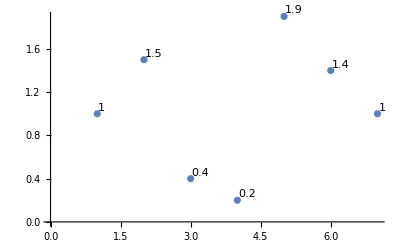

-Graphics3D-

```mathematica
d1 = Table[{Cos[x/2]//N, Sin[x/2]//N, 1},{x,0,6}];

chorddist[pts_]:=Accumulate[Table[EuclideanDistance[pts[[i]],pts[[i+1]]],{i,Length[pts]-1}]];
chordparam[pts_]:=N[Prepend[chorddist[pts]/Last[chorddist[pts]],0]];
controlparam[n_,pts_,param_]:=  Join[Table[0,{i,0,0}],Table[Sum[param[[i]],{i,j,Length[pts]-n+j}]/(Length[pts]-n+1),{j,2,n-1}],Table[1,{i,0,0}]];
knott[d_,ctrlparam_]:=Join[Table[0,{i,0,d}],Table[Sum[ctrlparam[[i]],{i,j,j+d-1}]/d,{j,2,Length[ctrlparam]-d}], Table[1,{i,0,d}]];
basis[pts_,n_,d_,knot_]:=With[{param=chordparam[pts]},Table[BSplineBasis[{d,knot},j-1,param[[i]]],{i,Length[param]},{j,n}]];
curve[pts_,knot_,d_,t_]:=Sum[BSplineBasis[{d,knot},i,t]*pts[[i+1]],{i,0,(Length[pts]-1)}];
curve3dto2d[pts_,knot_,d_,t_]:=(value=Sum[BSplineBasis[{d,knot},i,t]*pts[[i+1]],{i,0,(Length[pts]-1)}];Return[value/value[[3]]]);

d=3;
numcontrolpoint=6;
d13d=d1;
weight={1,1.5,0.4,0.2,1.9,1.4,1};
Do[d13d[[i]]=d1[[i]]*weight[[i]],{i,1,7}];

ti=chordparam[d13d];

controlparameter=controlparam[numcontrolpoint,d13d,ti];
knot=knott[d,controlparameter];

controlpts=LeastSquares[basis[d13d,numcontrolpoint,d,knot],d13d];

conparam=chordparam[controlpts];
conknot=knott[d,conparam];

datapointsplot=Graphics3D[{Black,PointSize[0.015],Point[d1],PointSize[0.02],Point[d1[[1]]],Line[d1]}];

curve3d=ParametricPlot3D[curve[controlpts,conknot,d,t],{t,0,1}, PlotStyle->Red];
curve2d=ParametricPlot3D[curve3dto2d[controlpts,conknot,d,t],{t,0,1}, PlotStyle->Green];

point3d=Graphics3D[{Blue,PointSize[0.015],Point[d13d],PointSize[0.02],Point[d13d[[1]]],Dashed,Line[d13d]}];
control3D=Graphics3D[{Cyan,PointSize[0.015],Point[controlpts],PointSize[0.02],Point[controlpts[[1]]],Dashed,Line[controlpts]}];

ListPlot[Labeled[#,#]&/@weight]
Show[{curve2d,curve3d,datapointsplot,point3d,control3D},Axes->True,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

Section2:
1. Given a 2D data points
2. Assign chord length parameter t_i to 2D data points
3.  First, we need to generate clamped knots for a given number of control points and degrees. Then, use BSplineBasis[] to define the B-spline basis matrix for least squares. Finally, use the LeastSquares[] to get the 2D control points. 
4. Compute random weights to lift the 2D control points into 3D control points
5. Use 3D control points to find the BSpline curve on 3D and project this curve back to 2D BSpline curve.

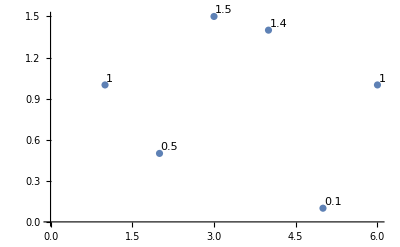

-Graphics3D-

```mathematica
d1 = Table[{Cos[x/2]//N, Sin[x/2]//N, 1},{x,0,6}];

chorddist[pts_]:=Accumulate[Table[EuclideanDistance[pts[[i]],pts[[i+1]]],{i,Length[pts]-1}]];
chordparam[pts_]:=N[Prepend[chorddist[pts]/Last[chorddist[pts]],0]];
controlparam[n_,pts_,param_]:=  Join[Table[0,{i,0,0}],Table[Sum[param[[i]],{i,j,Length[pts]-n+j}]/(Length[pts]-n+1),{j,2,n-1}],Table[1,{i,0,0}]];
knott[d_,ctrlparam_]:=Join[Table[0,{i,0,d}],Table[Sum[ctrlparam[[i]],{i,j,j+d-1}]/d,{j,2,Length[ctrlparam]-d}], Table[1,{i,0,d}]];
basis[pts_,n_,d_,knot_]:=With[{param=chordparam[pts]},Table[BSplineBasis[{d,knot},j-1,param[[i]]],{i,Length[param]},{j,n}]];
curve[pts_,knot_,d_,t_]:=Sum[BSplineBasis[{d,knot},i,t]*pts[[i+1]],{i,0,(Length[pts]-1)}];
curve3dto2d[pts_,knot_,d_,t_]:=(value=Sum[BSplineBasis[{d,knot},i,t]*pts[[i+1]],{i,0,(Length[pts]-1)}];Return[value/value[[3]]]);

d=3;
numcontrolpoint=6;
ti=chordparam[d1];

controlparameter=controlparam[numcontrolpoint,d1,ti];
knot=knott[d,controlparameter];

controlpts=LeastSquares[basis[d1,numcontrolpoint,d,knot],d1];
controlpts3D=controlpts;
weight={1,0.5,1.5,1.4,0.1,1};
Do[controlpts3D[[i]]=controlpts[[i]]*weight[[i]],{i,1,6}];

conparam=chordparam[controlpts3D];
conknot=knott[d,conparam];

datapointsplot=Graphics3D[{Black,PointSize[0.015],Point[d1],PointSize[0.02],Point[d1[[1]]],Line[d1]}];

control2D=Graphics3D[{Blue,PointSize[0.015],Point[controlpts],PointSize[0.02],Point[controlpts[[1]]],Dashed,Line[controlpts]}];
control3D=Graphics3D[{Cyan,PointSize[0.015],Point[controlpts3D],PointSize[0.02],Point[controlpts3D[[1]]],Dashed,Line[controlpts3D]}];

curve3d=ParametricPlot3D[curve[controlpts3D,conknot,d,t],{t,0,1}, PlotStyle->Red];
curve2d=ParametricPlot3D[curve3dto2d[controlpts3D,conknot,d,t],{t,0,1}, PlotStyle->Green];

ListPlot[Labeled[#,#]&/@weight]
Show[{curve3d,curve2d,datapointsplot,control2D,control3D},Axes->True,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

- Discussion: 
I am a little confused whether I should lift the 2D data to 3D first or do the least square first. So, I do 2 different procedures and both of the results look fine. The difference between this 2 methods is that the chord length parameter value is assigned to 2D and 3D respectively. But the result curve of the first method (section 1) looks more fit with the original 2D data.